## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PGK";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
(*pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef_1/";*)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy_r.csv";

mainFolder = "fit_PGK_Modified_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

((13dpg)^c+adp^c⇌(3pg)^c+atp^c)^PGK

random;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 13dpg | Null
adp | Null | 1490.64 | 1416.1
1565.17 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.000085 | 0.00008075
0.00008925 |  | M | 7 | 25 |  | 
1 | 13dpg | 0.000011 | 0.00001045
0.00001155 |  | M | 7 | 25 |  | 
1 | atp | 0.0035 | 0.003325
0.003675 |  | M | 7 | 25 |  | 
1 | 3pg | 0.0025 | 0.002375
0.002625 |  | M | 7 | 25 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | Null
13dpg | Null | 2327.18 | 2210.82
2443.54 | 1/s | 7 | 37 |  | 
1 | 3pg | Null
atp | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((13dpg)^c+adp^c⇌(3pg)^c+atp^c)^PGK

random;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 13dpg | Null
adp | Null | 1490.64 | 1416.1
1565.17 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.000085 | 0.00008075
0.00008925 |  | M | 7 | 25 |  | 
1 | 13dpg | 0.000011 | 0.00001045
0.00001155 |  | M | 7 | 25 |  | 
1 | atp | 0.0035 | 0.003325
0.003675 |  | M | 7 | 25 |  | 
1 | 3pg | 0.0025 | 0.002375
0.002625 |  | M | 7 | 25 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | Null
13dpg | Null | 2327.18 | 2210.82
2443.54 | 1/s | 7 | 37 |  | 
1 | 3pg | Null
atp | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PGK[c] + 13dpg[c] <=> E_PGK[c]&13dpg",
				"E_PGK[c]&13dpg + adp[c] <=> E_PGK[c]&13dpg&adp",

				"E_PGK[c] + adp[c] <=> E_PGK[c]&adp",
				"E_PGK[c]&adp + 13dpg[c] <=> E_PGK[c]&13dpg&adp",

				"E_PGK[c]&13dpg&adp <=> E_PGK[c]&3pg&atp",

				"E_PGK[c]&3pg&atp <=> E_PGK[c]&3pg + atp[c]",
				"E_PGK[c]&3pg <=> E_PGK[c] + 3pg[c]",
				
				"E_PGK[c]&3pg&atp <=> E_PGK[c]&atp + 3pg[c]",
				"E_PGK[c]&atp <=> E_PGK[c] + atp[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PGK^c)_^+adp^c⇌(PGK^c&adp^c)_^)^PGK1,((PGK^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c)_^)^PGK2,((PGK^c&atp^c)_^⇌(PGK^c)_^+atp^c)^PGK3,((PGK^c&(3pg)^c)_^⇌(PGK^c)_^+(3pg)^c)^PGK4,((PGK^c&adp^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK5,((PGK^c&(13dpg)^c)_^+adp^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK6,((PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&atp^c)_^+(3pg)^c)^PGK7,((PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&(3pg)^c)_^+atp^c)^PGK8,((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGK^c)_^+adp^c⇌(PGK^c&adp^c)_^)^PGK1, ((PGK^c&adp^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK5, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9, Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&(3pg)^c)_^+atp^c, PGK8], Overscript[(PGK^c&(3pg)^c)_^⇌(PGK^c)_^+(3pg)^c, PGK4]};
catalyticReactionsSet2={((PGK^c)_^+adp^c⇌(PGK^c&adp^c)_^)^PGK1, ((PGK^c&adp^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK5, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9, Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&atp^c)_^+(3pg)^c, PGK7], Overscript[(PGK^c&atp^c)_^⇌(PGK^c)_^+atp^c, PGK3]};
catalyticReactionsSet3={((PGK^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c)_^)^PGK2, ((PGK^c&(13dpg)^c)_^+adp^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK6, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9,  Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&(3pg)^c)_^+atp^c, PGK8], Overscript[(PGK^c&(3pg)^c)_^⇌(PGK^c)_^+(3pg)^c, PGK4]};
catalyticReactionsSet4={((PGK^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c)_^)^PGK2, ((PGK^c&(13dpg)^c)_^+adp^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK6, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9, Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&atp^c)_^+(3pg)^c, PGK7], Overscript[(PGK^c&atp^c)_^⇌(PGK^c)_^+atp^c, PGK3]};
catalyticReactionsSetsList = {catalyticReactionsSet1, catalyticReactionsSet2, catalyticReactionsSet3, catalyticReactionsSet4};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PGK^c&(13dpg)^c&adp^c)_^-((PGK^c&(3pg)^c&atp^c)_^)/K_PGK9) Volume_c k_PGK9^⟶}

Volume_c (-(PGK^c&(3pg)^c&atp^c)_^ k_PGK9^⟵+(PGK^c&(13dpg)^c&adp^c)_^ k_PGK9^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
Variables[haldaneRatiosList[[1]]][[1]]
haldaneRatiosList[[1]]
```

k_PGK1^⟵

(k_PGK1^⟶ k_PGK4^⟶ k_PGK5^⟶ k_PGK8^⟶ k_PGK9^⟶)/(k_PGK1^⟵ k_PGK4^⟵ k_PGK5^⟵ k_PGK8^⟵ k_PGK9^⟵)

```mathematica
Variables[haldaneRatiosList[[1]]][[1]]
keqValCur =1490.635085;
haldaneSub = Solve[keqValCur== haldaneRatiosList[[1]],Variables[haldaneRatiosList[[1]]][[1]]];
haldaneSub[[1,1]]
haldaneSub2 = Solve[keqValCur== haldaneRatiosList[[2]],Variables[haldaneRatiosList[[2]]][[1]]];
haldaneSub2[[1,1]]
haldaneSub3 = Solve[keqValCur== haldaneRatiosList[[3]],Variables[haldaneRatiosList[[3]]][[1]]];
haldaneSub3[[1,1]]
haldaneSub4 = Solve[keqValCur== haldaneRatiosList[[4]],Variables[haldaneRatiosList[[4]]][[1]]];
haldaneSub4[[1,1]]
```

k_PGK1^⟵

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

k_PGK1^⟵→(0.000670855 k_PGK1^⟶ k_PGK4^⟶ k_PGK5^⟶ k_PGK8^⟶ k_PGK9^⟶)/(k_PGK4^⟵ k_PGK5^⟵ k_PGK8^⟵ k_PGK9^⟵)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

k_PGK1^⟵→(0.000670855 k_PGK1^⟶ k_PGK3^⟶ k_PGK5^⟶ k_PGK7^⟶ k_PGK9^⟶)/(k_PGK3^⟵ k_PGK5^⟵ k_PGK7^⟵ k_PGK9^⟵)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

k_PGK2^⟵→(0.000670855 k_PGK2^⟶ k_PGK4^⟶ k_PGK6^⟶ k_PGK8^⟶ k_PGK9^⟶)/(k_PGK4^⟵ k_PGK6^⟵ k_PGK8^⟵ k_PGK9^⟵)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

k_PGK2^⟵→(0.000670855 k_PGK2^⟶ k_PGK3^⟶ k_PGK6^⟶ k_PGK7^⟶ k_PGK9^⟶)/(k_PGK3^⟵ k_PGK6^⟵ k_PGK7^⟵ k_PGK9^⟵)

```mathematica
flux = 0.00382;
FluxExpression = absoluteFlux /. {metabolite["13dpg", "c"] -> 0.0000069,metabolite["adp","c"]-> 0.000285,
metabolite["3pg","c"]-> 0.000000108,metabolite["atp","c"]-> 0.0006817, parameter["PGK_total"] -> 0.0000949803694413746, parameter["Volume", "c"] -> 1};
```

```mathematica
FluxExpression2 = parameter["v", "PGK"] /. FluxExpression/.haldaneSub[[1,1]];
FluxExpression3 = parameter["v", "PGK"] /. FluxExpression/.haldaneSub2[[1,1]];
FluxExpression4 = parameter["v", "PGK"] /. FluxExpression/.haldaneSub3[[1,1]];
FluxExpression5 = parameter["v", "PGK"] /. FluxExpression/.haldaneSub4[[1,1]];
```

```mathematica
haldaneSub2[[1,1]]
```

k_PGK1^⟵→(0.000670855 k_PGK1^⟶ k_PGK3^⟶ k_PGK5^⟶ k_PGK7^⟶ k_PGK9^⟶)/(k_PGK3^⟵ k_PGK5^⟵ k_PGK7^⟵ k_PGK9^⟵)

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{3,FluxExpression2,flux,{0.9*flux,1.1*flux}},{3,FluxExpression3,flux,{0.9*flux,1.1*flux}},{3,FluxExpression4,flux,{0.9*flux,1.1*flux}},{3,FluxExpression5,flux,{0.9*flux,1.1*flux}}};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	13dpg[c]	adp[c]	atp[c]	3pg[c]	param_PGK_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_1.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_1.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_1.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_1.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_1.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_1.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_1.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_1.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_1.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_1.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_1.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_2.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_2.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_2.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_2.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_2.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_2.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_2.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_2.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_2.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_2.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_2.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_3.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_3.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_3.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_3.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_3.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_3.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_3.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_3.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_3.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_3.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_3.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_4.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_4.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_4.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_4.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_4.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_4.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_4.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_4.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_4.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_4.txt"	1490.635085
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_4.txt"	1490.635085
1	1	8.500000000000002e-6	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_adp.txt"	0.09090909090909091
1	1	0.000013471592135919474	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_adp.txt"	0.13680688860321008
1	1	0.000021351034667831454	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_adp.txt"	0.20076000891310192
1	1	0.000033839109497047245	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_adp.txt"	0.2847472489508013
1	1	0.00005363137428081642	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_adp.txt"	0.3868631798468569
1	1	0.00008500000000000002	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_adp.txt"	0.5000000000000001
1	1	0.00013471592135919474	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_adp.txt"	0.6131368201531432
1	1	0.00021351034667831454	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_adp.txt"	0.7152527510491988
1	1	0.00033839109497047284	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_adp.txt"	0.7992399910868982
1	1	0.0005363137428081642	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_adp.txt"	0.86319311139679
1	1	0.0008500000000000003	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_adp.txt"	0.9090909090909092
1	1.100000000000001e-6	1	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_13dpg.txt"	0.09090909090909097
1	1.7433825117072269e-6	1	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_13dpg.txt"	0.13680688860321014
1	2.7630750746605424e-6	1	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_13dpg.txt"	0.200760008913102
1	4.37917887608847e-6	1	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_13dpg.txt"	0.2847472489508014
1	6.940530789282128e-6	1	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_13dpg.txt"	0.38686317984685703
1	0.000011000000000000008	1	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_13dpg.txt"	0.5000000000000002
1	0.00001743382511707227	1	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_13dpg.txt"	0.6131368201531434
1	0.000027630750746605424	1	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_13dpg.txt"	0.7152527510491988
1	0.00004379178876088469	1	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_13dpg.txt"	0.7992399910868982
1	0.00006940530789282128	1	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_13dpg.txt"	0.8631931113967901
1	0.00011000000000000009	1	0	0	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_13dpg.txt"	0.9090909090909092
1	0	0	0.00035000000000000005	1	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_atp.txt"	0.09090909090909091
1	0	0	0.0005547126173613899	1	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_atp.txt"	0.13680688860321005
1	0	0	0.000879160251028353	1	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_atp.txt"	0.20076000891310175
1	0	0	0.0013933750969372409	1	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_atp.txt"	0.28474724895080145
1	0	0	0.0022083507056806758	1	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_atp.txt"	0.38686317984685686
1	0	0	0.0035	1	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_atp.txt"	0.5
1	0	0	0.0055471261736139	1	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_atp.txt"	0.6131368201531431
1	0	0	0.008791602510283538	1	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_atp.txt"	0.7152527510491987
1	0	0	0.013933750969372407	1	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_atp.txt"	0.7992399910868984
1	0	0	0.022083507056806766	1	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_atp.txt"	0.8631931113967901
1	0	0	0.035	1	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_atp.txt"	0.9090909090909091
1	0	0	1	0.00024999999999999995	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_3pg.txt"	0.0909090909090909
1	0	0	1	0.0003962232981152784	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_3pg.txt"	0.13680688860321003
1	0	0	1	0.0006279716078773948	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_3pg.txt"	0.20076000891310167
1	0	0	1	0.0009952679263837431	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_3pg.txt"	0.2847472489508014
1	0	0	1	0.0015773933612004821	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_3pg.txt"	0.3868631798468568
1	0	0	1	0.002499999999999999	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_3pg.txt"	0.4999999999999999
1	0	0	1	0.0039622329811527844	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_3pg.txt"	0.6131368201531431
1	0	0	1	0.006279716078773954	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_3pg.txt"	0.7152527510491987
1	0	0	1	0.00995267926383743	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_3pg.txt"	0.7992399910868982
1	0	0	1	0.01577393361200483	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_3pg.txt"	0.8631931113967901
1	0	0	1	0.024999999999999994	1	7	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_3pg.txt"	0.9090909090909092
1	1	1	0	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateFor.txt"	2327.1785908390234
1	0	0	1	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_1.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_1.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_1.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_1.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_1.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_1.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_1.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_1.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_1.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_1.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_1.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_2.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_2.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_2.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_2.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_2.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_2.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_2.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_2.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_2.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_2.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_2.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_3.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_3.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_3.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_3.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_3.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_3.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_3.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_3.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_3.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_3.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_3.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_4.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_4.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_4.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_4.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_4.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_4.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_4.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_4.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_4.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_4.txt"	0.00382
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_4.txt"	0.00382

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	18
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_13dpg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_adp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_3pg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_atp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_2.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_3.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_4.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_2.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_3.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_4.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	18
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_13dpg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateFor_adp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_3pg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/relRateRev_atp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_2.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_3.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/haldaneRatio_4.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_2.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_3.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGK_Modified_MASSpy_typeII/input/customRatio_4.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

Traceback (most recent call last):
  File "/Users/guest/Desktop/internship stuff/MASSef/python_code/src/run_fit_rel.py", line 61, in <module>
    run_pso(pso_parameters, data_file_name, pso_summary_file_name, pso_ultimate_result_file_name)
  File "/Users/guest/Desktop/internship stuff/MASSef/python_code/src/pso_short_ver0091_rel_marta.py", line 544, in run_pso
    best_fitness_cutoff=best_fitness_cutoff_value)
  File "/Users/guest/Desktop/internship stuff/MASSef/python_code/src/ecspy_adapted/ec.py", line 360, in evolve
    initial_fit = evaluator(candidates=initial_cs, args=self._kwargs)
  File "/Users/guest/Desktop/internship stuff/MASSef/python_code/src/pso_short_ver0091_rel_marta.py", line 167, in evaluator
    {'_ec': self.logger, 'mp_evaluator': _evaluator, 'mp_num_cpus': num_Cpus})
  File "/Users/guest/Desktop/internship stuff/MASSef/python_code/src/pso_short_ver0091_rel_marta.py", line 124, in parallel_evaluation_mp
    return [r.get()[0] for r in results]
  File "/System/Library/Frameworks/Python.framework/Versions/2.7/lib/python2.7/multiprocessing/pool.py", line 567, in get
    raise self._value
AssertionError: Some predicted data points values are negative

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\PGK_PGK.dat⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 8.08972×10^-10 | 6.54436×10^-19 | 2.77665×10^-6 | 1.86273×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_1 | 8.08972×10^-10 | 6.54436×10^-19 | 2.77665×10^-6 | 1.86273×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_1 | 8.08972×10^-10 | 6.54436×10^-19 | 2.77665×10^-6 | 1.86273×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_1 | 8.08972×10^-10 | 6.54436×10^-19 | 2.77665×10^-6 | 1.86273×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_1 | 8.08972×10^-10 | 6.54436×10^-19 | 2.77665×10^-6 | 1.86273×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_1 | 8.08972×10^-10 | 6.54436×10^-19 | 2.77665×10^-6 | 1.86273×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_1 | 8.08972×10^-10 | 6.54436×10^-19 | 2.77665×10^-6 | 1.86273×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_1 | 8.08972×10^-10 | 6.54436×10^-19 | 2.77665×10^-6 | 1.86273×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_1 | 8.08972×10^-10 | 6.54436×10^-19 | 2.77665×10^-6 | 1.86273×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_1 | 8.08972×10^-10 | 6.54436×10^-19 | 2.77665×10^-6 | 1.86273×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_1 | 8.08972×10^-10 | 6.54436×10^-19 | 2.77665×10^-6 | 1.86273×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_2 | 6.23029×10^-10 | 3.88165×10^-19 | 2.13843×10^-6 | 1.43458×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_2 | 6.23029×10^-10 | 3.88165×10^-19 | 2.13843×10^-6 | 1.43458×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_2 | 6.23029×10^-10 | 3.88165×10^-19 | 2.13843×10^-6 | 1.43458×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_2 | 6.23029×10^-10 | 3.88165×10^-19 | 2.13843×10^-6 | 1.43458×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_2 | 6.23029×10^-10 | 3.88165×10^-19 | 2.13843×10^-6 | 1.43458×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_2 | 6.23029×10^-10 | 3.88165×10^-19 | 2.13843×10^-6 | 1.43458×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_2 | 6.23029×10^-10 | 3.88165×10^-19 | 2.13843×10^-6 | 1.43458×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_2 | 6.23029×10^-10 | 3.88165×10^-19 | 2.13843×10^-6 | 1.43458×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_2 | 6.23029×10^-10 | 3.88165×10^-19 | 2.13843×10^-6 | 1.43458×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_2 | 6.23029×10^-10 | 3.88165×10^-19 | 2.13843×10^-6 | 1.43458×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_2 | 6.23029×10^-10 | 3.88165×10^-19 | 2.13843×10^-6 | 1.43458×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_3 | 9.78972×10^-10 | 9.58387×10^-19 | 3.36014×10^-6 | 2.25417×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_3 | 9.78972×10^-10 | 9.58387×10^-19 | 3.36014×10^-6 | 2.25417×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_3 | 9.78972×10^-10 | 9.58387×10^-19 | 3.36014×10^-6 | 2.25417×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_3 | 9.78972×10^-10 | 9.58387×10^-19 | 3.36014×10^-6 | 2.25417×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_3 | 9.78972×10^-10 | 9.58387×10^-19 | 3.36014×10^-6 | 2.25417×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_3 | 9.78972×10^-10 | 9.58387×10^-19 | 3.36014×10^-6 | 2.25417×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_3 | 9.78972×10^-10 | 9.58387×10^-19 | 3.36014×10^-6 | 2.25417×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_3 | 9.78972×10^-10 | 9.58387×10^-19 | 3.36014×10^-6 | 2.25417×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_3 | 9.78972×10^-10 | 9.58387×10^-19 | 3.36014×10^-6 | 2.25417×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_3 | 9.78972×10^-10 | 9.58387×10^-19 | 3.36014×10^-6 | 2.25417×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_3 | 9.78972×10^-10 | 9.58387×10^-19 | 3.36014×10^-6 | 2.25417×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_4 | 4.53029×10^-10 | 2.05235×10^-19 | 1.55494×10^-6 | 1.04314×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_4 | 4.53029×10^-10 | 2.05235×10^-19 | 1.55494×10^-6 | 1.04314×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_4 | 4.53029×10^-10 | 2.05235×10^-19 | 1.55494×10^-6 | 1.04314×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_4 | 4.53029×10^-10 | 2.05235×10^-19 | 1.55494×10^-6 | 1.04314×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_4 | 4.53029×10^-10 | 2.05235×10^-19 | 1.55494×10^-6 | 1.04314×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_4 | 4.53029×10^-10 | 2.05235×10^-19 | 1.55494×10^-6 | 1.04314×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_4 | 4.53029×10^-10 | 2.05235×10^-19 | 1.55494×10^-6 | 1.04314×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_4 | 4.53029×10^-10 | 2.05235×10^-19 | 1.55494×10^-6 | 1.04314×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_4 | 4.53029×10^-10 | 2.05235×10^-19 | 1.55494×10^-6 | 1.04314×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_4 | 4.53029×10^-10 | 2.05235×10^-19 | 1.55494×10^-6 | 1.04314×10^-7 | 1490.64 | 1490.64
1 | haldaneRatio_4 | 4.53029×10^-10 | 2.05235×10^-19 | 1.55494×10^-6 | 1.04314×10^-7 | 1490.64 | 1490.64
1 | relRateFor_adp | 0.0000137022 | 1.87751×10^-10 | 2.86819×10^-6 | 0.003155 | 0.0909091 | 0.0909062
1 | relRateFor_adp | 0.0000111467 | 1.24248×10^-10 | 3.51126×10^-6 | 0.00256658 | 0.136807 | 0.136803
1 | relRateFor_adp | 7.58577×10^-6 | 5.75439×10^-11 | 3.50662×10^-6 | 0.00174667 | 0.20076 | 0.200757
1 | relRateFor_adp | 2.90934×10^-6 | 8.46423×10^-12 | 1.90751×10^-6 | 0.000669897 | 0.284747 | 0.284745
1 | relRateFor_adp | 2.77658×10^-6 | 7.70939×10^-12 | 2.47334×10^-6 | 0.000639333 | 0.386863 | 0.386866
1 | relRateFor_adp | 9.07623×10^-6 | 8.2378×10^-11 | 0.0000104495 | 0.0020899 | 0.5 | 0.50001
1 | relRateFor_adp | 0.000015376 | 2.36421×10^-10 | 0.0000217082 | 0.00354051 | 0.613137 | 0.613159
1 | relRateFor_adp | 0.0000210621 | 4.43613×10^-10 | 0.0000346887 | 0.00484985 | 0.715253 | 0.715287
1 | relRateFor_adp | 0.0000257389 | 6.6249×10^-10 | 0.0000473691 | 0.00592677 | 0.79924 | 0.799287
1 | relRateFor_adp | 0.0000293001 | 8.58494×10^-10 | 0.0000582381 | 0.00674682 | 0.863193 | 0.863251
1 | relRateFor_adp | 0.0000318559 | 1.0148×10^-9 | 0.0000666851 | 0.00733536 | 0.909091 | 0.909158
1 | relRateFor_13dpg | 1.77284×10^-6 | 3.14297×10^-12 | 3.71101×10^-7 | 0.000408211 | 0.0909091 | 0.0909087
1 | relRateFor_13dpg | 1.44206×10^-6 | 2.07954×10^-12 | 4.54262×10^-7 | 0.000332046 | 0.136807 | 0.136806
1 | relRateFor_13dpg | 9.81157×10^-7 | 9.62668×10^-13 | 4.53556×10^-7 | 0.000225919 | 0.20076 | 0.20076
1 | relRateFor_13dpg | 3.7587×10^-7 | 1.41278×10^-13 | 2.46441×10^-7 | 0.0000865472 | 0.284747 | 0.284747
1 | relRateFor_13dpg | 3.60067×10^-7 | 1.29648×10^-13 | 3.20742×10^-7 | 0.0000829085 | 0.386863 | 0.386864
1 | relRateFor_13dpg | 1.17543×10^-6 | 1.38162×10^-12 | 1.35326×10^-6 | 0.000270652 | 0.5 | 0.500001
1 | relRateFor_13dpg | 1.99077×10^-6 | 3.96318×10^-12 | 2.81058×10^-6 | 0.000458394 | 0.613137 | 0.61314
1 | relRateFor_13dpg | 2.72668×10^-6 | 7.43478×10^-12 | 4.49067×10^-6 | 0.000627843 | 0.715253 | 0.715257
1 | relRateFor_13dpg | 3.33191×10^-6 | 1.11016×10^-11 | 6.1318×10^-6 | 0.000767203 | 0.79924 | 0.799246
1 | relRateFor_13dpg | 3.79272×10^-6 | 1.43848×10^-11 | 7.53836×10^-6 | 0.000873311 | 0.863193 | 0.863201
1 | relRateFor_13dpg | 4.12338×10^-6 | 1.70023×10^-11 | 8.63134×10^-6 | 0.000949448 | 0.909091 | 0.9091
1 | relRateRev_atp | 0.000874686 | 7.65075×10^-7 | 0.00018291 | 0.201201 | 0.0909091 | 0.0907262
1 | relRateRev_atp | 0.000711203 | 5.05809×10^-7 | 0.000223852 | 0.163626 | 0.136807 | 0.136583
1 | relRateRev_atp | 0.00048334 | 2.33617×10^-7 | 0.000223308 | 0.111231 | 0.20076 | 0.200537
1 | relRateRev_atp | 0.00018399 | 3.38522×10^-8 | 0.000120608 | 0.0423562 | 0.284747 | 0.284627
1 | relRateRev_atp | 0.000180089 | 3.24321×10^-8 | 0.000160454 | 0.0414757 | 0.386863 | 0.387024
1 | relRateRev_atp | 0.000583482 | 3.40451×10^-7 | 0.00067221 | 0.134442 | 0.5 | 0.500672
1 | relRateRev_atp | 0.000986597 | 9.73373×10^-7 | 0.00139446 | 0.22743 | 0.613137 | 0.614531
1 | relRateRev_atp | 0.00134956 | 1.8213×10^-6 | 0.00222608 | 0.31123 | 0.715253 | 0.717479
1 | relRateRev_atp | 0.00164616 | 2.70985×10^-6 | 0.00303521 | 0.379762 | 0.79924 | 0.802275
1 | relRateRev_atp | 0.00186849 | 3.49124×10^-6 | 0.00372176 | 0.431162 | 0.863193 | 0.866915
1 | relRateRev_atp | 0.00202199 | 4.08846×10^-6 | 0.00424242 | 0.466667 | 0.909091 | 0.913333
1 | relRateRev_3pg | 0.000399212 | 1.5937×10^-7 | 0.000083527 | 0.0918797 | 0.0909091 | 0.0908256
1 | relRateRev_3pg | 0.000324224 | 1.05121×10^-7 | 0.000102096 | 0.0746276 | 0.136807 | 0.136705
1 | relRateRev_3pg | 0.000219717 | 4.82755×10^-8 | 0.000101542 | 0.0505789 | 0.20076 | 0.200658
1 | relRateRev_3pg | 0.0000824327 | 6.79515×10^-9 | 0.0000540423 | 0.018979 | 0.284747 | 0.284693
1 | relRateRev_3pg | 0.0000845427 | 7.14748×10^-9 | 0.0000753168 | 0.0194686 | 0.386863 | 0.386938
1 | relRateRev_3pg | 0.000269614 | 7.26917×10^-8 | 0.000310501 | 0.0621002 | 0.5 | 0.500311
1 | relRateRev_3pg | 0.000454764 | 2.06811×10^-7 | 0.000642372 | 0.104768 | 0.613137 | 0.613779
1 | relRateRev_3pg | 0.000621946 | 3.86817×10^-7 | 0.00102504 | 0.143311 | 0.715253 | 0.716278
1 | relRateRev_3pg | 0.000759497 | 5.76836×10^-7 | 0.00139894 | 0.175034 | 0.79924 | 0.800639
1 | relRateRev_3pg | 0.000864266 | 7.46955×10^-7 | 0.0017195 | 0.199203 | 0.863193 | 0.864913
1 | relRateRev_3pg | 0.000939472 | 8.82607×10^-7 | 0.00196869 | 0.216555 | 0.909091 | 0.91106
1 | absRateFor | 2.59853×10^-7 | 6.75236×10^-14 | 0.00139243 | 0.0000598334 | 2327.18 | 2327.18
1 | absRateFor | 2.59853×10^-7 | 6.75236×10^-14 | 0.00139243 | 0.0000598334 | 2327.18 | 2327.18
1 | absRateFor | 2.59853×10^-7 | 6.75236×10^-14 | 0.00139243 | 0.0000598334 | 2327.18 | 2327.18
1 | absRateFor | 2.59853×10^-7 | 6.75236×10^-14 | 0.00139243 | 0.0000598334 | 2327.18 | 2327.18
1 | absRateFor | 2.59853×10^-7 | 6.75236×10^-14 | 0.00139243 | 0.0000598334 | 2327.18 | 2327.18
1 | absRateFor | 2.59853×10^-7 | 6.75236×10^-14 | 0.00139243 | 0.0000598334 | 2327.18 | 2327.18
1 | absRateFor | 2.59853×10^-7 | 6.75236×10^-14 | 0.00139243 | 0.0000598334 | 2327.18 | 2327.18
1 | absRateFor | 2.59853×10^-7 | 6.75236×10^-14 | 0.00139243 | 0.0000598334 | 2327.18 | 2327.18
1 | absRateFor | 2.59853×10^-7 | 6.75236×10^-14 | 0.00139243 | 0.0000598334 | 2327.18 | 2327.18
1 | absRateFor | 2.59853×10^-7 | 6.75236×10^-14 | 0.00139243 | 0.0000598334 | 2327.18 | 2327.18
1 | absRateFor | 2.59853×10^-7 | 6.75236×10^-14 | 0.00139243 | 0.0000598334 | 2327.18 | 2327.18
1 | absRateRev | 1.7952×10^-7 | 3.22274×10^-14 | 0.0000124124 | 0.000041336 | 30.0281 | 30.0281
1 | absRateRev | 1.7952×10^-7 | 3.22274×10^-14 | 0.0000124124 | 0.000041336 | 30.0281 | 30.0281
1 | absRateRev | 1.7952×10^-7 | 3.22274×10^-14 | 0.0000124124 | 0.000041336 | 30.0281 | 30.0281
1 | absRateRev | 1.7952×10^-7 | 3.22274×10^-14 | 0.0000124124 | 0.000041336 | 30.0281 | 30.0281
1 | absRateRev | 1.7952×10^-7 | 3.22274×10^-14 | 0.0000124124 | 0.000041336 | 30.0281 | 30.0281
1 | absRateRev | 1.7952×10^-7 | 3.22274×10^-14 | 0.0000124124 | 0.000041336 | 30.0281 | 30.0281
1 | absRateRev | 1.7952×10^-7 | 3.22274×10^-14 | 0.0000124124 | 0.000041336 | 30.0281 | 30.0281
1 | absRateRev | 1.7952×10^-7 | 3.22274×10^-14 | 0.0000124124 | 0.000041336 | 30.0281 | 30.0281
1 | absRateRev | 1.7952×10^-7 | 3.22274×10^-14 | 0.0000124124 | 0.000041336 | 30.0281 | 30.0281
1 | absRateRev | 1.7952×10^-7 | 3.22274×10^-14 | 0.0000124124 | 0.000041336 | 30.0281 | 30.0281
1 | absRateRev | 1.7952×10^-7 | 3.22274×10^-14 | 0.0000124124 | 0.000041336 | 30.0281 | 30.0281
3 | customRatio_1 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_1 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_1 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_1 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_1 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_1 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_1 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_1 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_1 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_1 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_1 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_2 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_2 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_2 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_2 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_2 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_2 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_2 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_2 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_2 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_2 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_2 | 4.47264×10^-11 | 2.00045×10^-21 | 3.93408×10^-13 | 1.02986×10^-8 | 0.00382 | 0.00382
3 | customRatio_3 | 9.75035×10^-10 | 9.50694×10^-19 | 8.57629×10^-12 | 2.2451×10^-7 | 0.00382 | 0.00382
3 | customRatio_3 | 9.75035×10^-10 | 9.50694×10^-19 | 8.57629×10^-12 | 2.2451×10^-7 | 0.00382 | 0.00382
3 | customRatio_3 | 9.75035×10^-10 | 9.50694×10^-19 | 8.57629×10^-12 | 2.2451×10^-7 | 0.00382 | 0.00382
3 | customRatio_3 | 9.75035×10^-10 | 9.50694×10^-19 | 8.57629×10^-12 | 2.2451×10^-7 | 0.00382 | 0.00382
3 | customRatio_3 | 9.75035×10^-10 | 9.50694×10^-19 | 8.57629×10^-12 | 2.2451×10^-7 | 0.00382 | 0.00382
3 | customRatio_3 | 9.75035×10^-10 | 9.50694×10^-19 | 8.57629×10^-12 | 2.2451×10^-7 | 0.00382 | 0.00382
3 | customRatio_3 | 9.75035×10^-10 | 9.50694×10^-19 | 8.57629×10^-12 | 2.2451×10^-7 | 0.00382 | 0.00382
3 | customRatio_3 | 9.75035×10^-10 | 9.50694×10^-19 | 8.57629×10^-12 | 2.2451×10^-7 | 0.00382 | 0.00382
3 | customRatio_3 | 9.75035×10^-10 | 9.50694×10^-19 | 8.57629×10^-12 | 2.2451×10^-7 | 0.00382 | 0.00382
3 | customRatio_3 | 9.75035×10^-10 | 9.50694×10^-19 | 8.57629×10^-12 | 2.2451×10^-7 | 0.00382 | 0.00382
3 | customRatio_3 | 9.75035×10^-10 | 9.50694×10^-19 | 8.57629×10^-12 | 2.2451×10^-7 | 0.00382 | 0.00382
3 | customRatio_4 | 3.85783×10^-10 | 1.48828×10^-19 | 3.3933×10^-12 | 8.88297×10^-8 | 0.00382 | 0.00382
3 | customRatio_4 | 3.85783×10^-10 | 1.48828×10^-19 | 3.3933×10^-12 | 8.88297×10^-8 | 0.00382 | 0.00382
3 | customRatio_4 | 3.85783×10^-10 | 1.48828×10^-19 | 3.3933×10^-12 | 8.88297×10^-8 | 0.00382 | 0.00382
3 | customRatio_4 | 3.85783×10^-10 | 1.48828×10^-19 | 3.3933×10^-12 | 8.88297×10^-8 | 0.00382 | 0.00382
3 | customRatio_4 | 3.85783×10^-10 | 1.48828×10^-19 | 3.3933×10^-12 | 8.88297×10^-8 | 0.00382 | 0.00382
3 | customRatio_4 | 3.85783×10^-10 | 1.48828×10^-19 | 3.3933×10^-12 | 8.88297×10^-8 | 0.00382 | 0.00382
3 | customRatio_4 | 3.85783×10^-10 | 1.48828×10^-19 | 3.3933×10^-12 | 8.88297×10^-8 | 0.00382 | 0.00382
3 | customRatio_4 | 3.85783×10^-10 | 1.48828×10^-19 | 3.3933×10^-12 | 8.88297×10^-8 | 0.00382 | 0.00382
3 | customRatio_4 | 3.85783×10^-10 | 1.48828×10^-19 | 3.3933×10^-12 | 8.88297×10^-8 | 0.00382 | 0.00382
3 | customRatio_4 | 3.85783×10^-10 | 1.48828×10^-19 | 3.3933×10^-12 | 8.88297×10^-8 | 0.00382 | 0.00382
3 | customRatio_4 | 3.85783×10^-10 | 1.48828×10^-19 | 3.3933×10^-12 | 8.88297×10^-8 | 0.00382 | 0.00382

### Simulated Data and Best Fit Data Plot

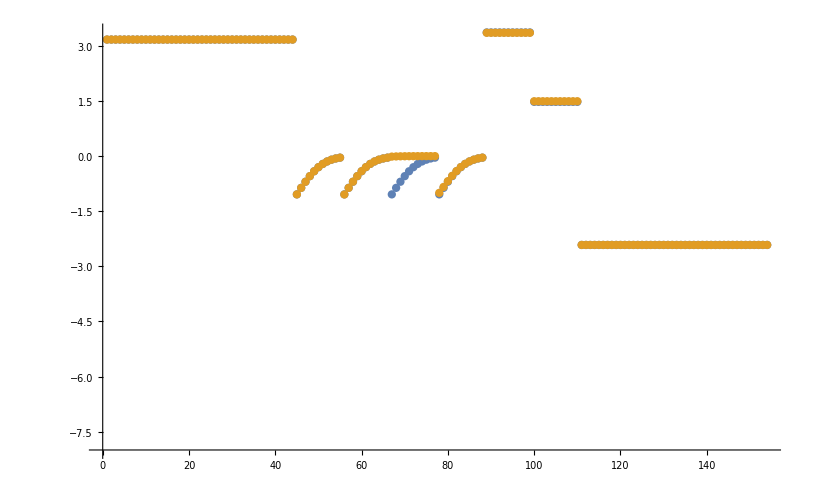

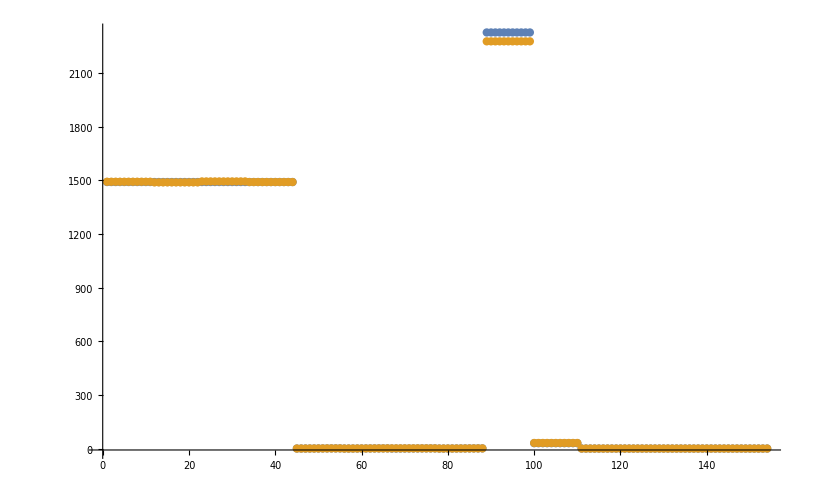

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

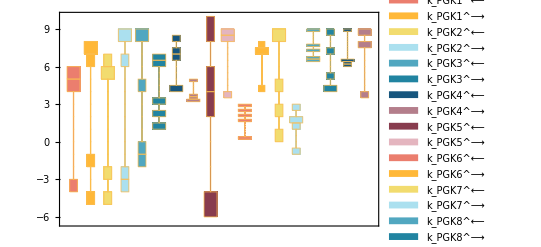

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[1;;5,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

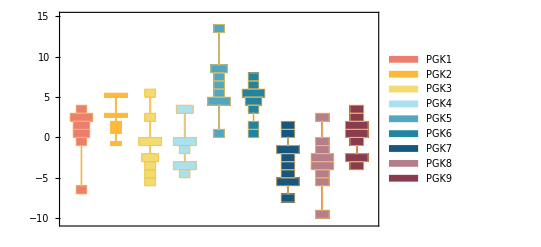

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

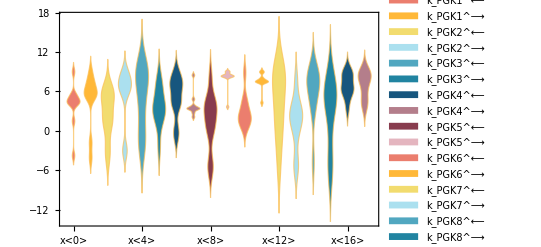

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

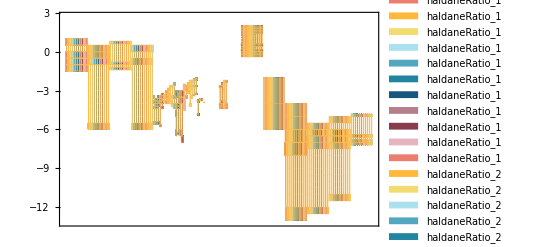

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

#### Cluster Parameters

```mathematica
(*clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->0.0001}}];(**)*)
clusters=FindClusters[Log10[filteredDataList[[1;;6,2]]],Method->{"Optimize","Iterations"->2}];
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

4.27155 | 6.30045 | 6.06795 | 6.97723 | 4.3414 | 1.25359 | 8.07066 | 4.81558 | 3.97826 | 8.33067 | 2.01237 | 7.48439 | 4.42819 | 1.80731 | 6.49242 | 4.04055 | 6.46501 | 8.96583

#### Parameter Cluster Plots (Optional)

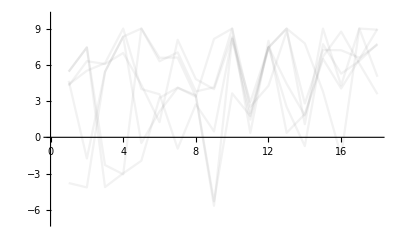

{-Graphics-}

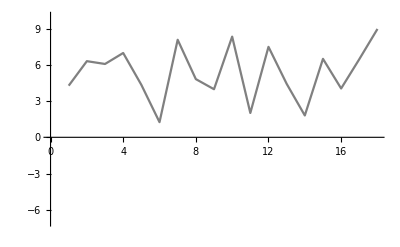

```mathematica
ListPlot[Log10[filteredDataList[[1;;6,2]]],"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]](*All parameter sets*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]]&/@clusters
(*All parameter set clusters*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[1,Gray]]&/@finalClusterParams(*Representative parameter sets*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.000085 | 0.0000849964 | 0.00417936
0.000011 | 0.0000109999 | 0.000541297
0.0035 | 0.00349065 | 0.26707
0.0025 | 0.0024969 | 0.123813

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
2327.18 | 2327.18 | 0.0000598334
30.0281 | 30.0281 | 0.000041336

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
1490.64 | 1490.64 | 1.86273×10^-7

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
1490.64 | 1490.64 | 1.86273×10^-7

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

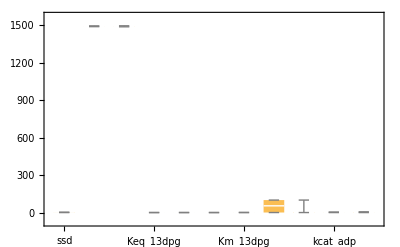

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

## Export data

```mathematica
directoryExport = "/Users/guest/Desktop/internship stuff/MASSef/examples/"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 4;
```

/Users/guest/Desktop/internship stuff/MASSef/examples/

CreateDirectory::filex: /Users/guest/Desktop/internship stuff/MASSef/examples/pgk already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgk\rateconst_labels_pgk.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgk\S_pgk.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_PGK[c],E_PGK[c]&13dpg,E_PGK[c]&3pg,E_PGK[c]&adp,E_PGK[c]&atp,E_PGK[c]&13dpg&adp,13dpg[c],adp[c],atp[c],E_PGK[c]&3pg&atp,3pg[c]}

/Users/guest/Desktop/internship stuff/MASSef/examples/pgk\species_pgk.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{PGK1: adp[c] + E_PGK[c] <=> E_PGK[c]&adp,PGK2: 13dpg[c] + E_PGK[c] <=> E_PGK[c]&13dpg,PGK3: E_PGK[c]&atp <=> atp[c] + E_PGK[c],PGK4: E_PGK[c]&3pg <=> 3pg[c] + E_PGK[c],PGK5: 13dpg[c] + E_PGK[c]&adp <=> E_PGK[c]&13dpg&adp,PGK6: adp[c] + E_PGK[c]&13dpg <=> E_PGK[c]&13dpg&adp,PGK7: E_PGK[c]&3pg&atp <=> 3pg[c] + E_PGK[c]&atp,PGK8: E_PGK[c]&3pg&atp <=> atp[c] + E_PGK[c]&3pg,PGK9: E_PGK[c]&13dpg&adp <=> E_PGK[c]&3pg&atp}

/Users/guest/Desktop/internship stuff/MASSef/examples/pgk\reactions_pgk.txt

```mathematica
solEnz = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_PGK[c],E_PGK[c]&13dpg,E_PGK[c]&3pg,E_PGK[c]&adp,E_PGK[c]&atp,E_PGK[c]&13dpg&adp,E_PGK[c]&3pg&atp}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((k_PGK3_fwd*(k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK6_rev*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_PGK_total*param_Volume_c**5*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK6_rev*param_Volume_c**2*(-(k_PGK2_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - adp(c)*k_PGK6_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3))) + (k_PGK2_rev + adp(c)*k_PGK6_fwd)*param_Volume_c*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*(k_PGK5_rev + k_PGK6_rev + k_PGK9_fwd)*param_Volume_c**2*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3)) - k_PGK5_rev*param_Volume_c*(-(k_PGK1_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3)))))/((-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK6_rev*param_Volume_c**2*(-(k_PGK2_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - adp(c)*k_PGK6_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3))) + (k_PGK2_rev + adp(c)*k_PGK6_fwd)*param_Volume_c*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*(k_PGK5_rev + k_PGK6_rev + k_PGK9_fwd)*param_Volume_c**2*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3)) - k_PGK5_rev*param_Volume_c*(-(k_PGK1_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3))))*(k_PGK6_rev*param_Volume_c*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK9_rev*param_Volume_c**2*(-(3pg(c)*k_PGK4_rev*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)) - (k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) - (adp(c)*k_PGK1_fwd + 13dpg(c)*k_PGK2_fwd + atp(c)*k_PGK3_rev + 3pg(c)*k_PGK4_rev)*param_Volume_c))) - adp(c)*k_PGK1_fwd*param_Volume_c*(-((k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**2*(k_PGK1_rev*param_Volume_c - k_PGK3_fwd*param_Volume_c)) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)))) - 13dpg(c)*k_PGK2_fwd*param_Volume_c*(-(k_PGK5_rev*param_Volume_c*(-((k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**2*(k_PGK1_rev*param_Volume_c - k_PGK3_fwd*param_Volume_c)) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)))) - (k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**3 + (k_PGK5_rev + k_PGK6_rev + k_PGK9_fwd)*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c))))) - (k_PGK6_rev*param_Volume_c*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK9_rev*param_Volume_c**2*(-(3pg(c)*k_PGK4_fwd*k_PGK4_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*param_Volume_c**3) - (k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c*(atp(c)*k_PGK3_fwd*k_PGK3_rev*param_Volume_c**2 - (adp(c)*k_PGK1_fwd + 13dpg(c)*k_PGK2_fwd + atp(c)*k_PGK3_rev + 3pg(c)*k_PGK4_rev)*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*param_Volume_c**2))) - adp(c)*k_PGK1_fwd*param_Volume_c*(-(k_PGK1_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3))) - 13dpg(c)*k_PGK2_fwd*param_Volume_c*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*(k_PGK5_rev + k_PGK6_rev + k_PGK9_fwd)*param_Volume_c**2*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3)) - k_PGK5_rev*param_Volume_c*(-(k_PGK1_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3))))*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK6_rev*param_Volume_c**2*(-((k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**2*(k_PGK2_rev*param_Volume_c - k_PGK3_fwd*param_Volume_c)) - adp(c)*k_PGK6_fwd*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)))) + (k_PGK2_rev + adp(c)*k_PGK6_fwd)*param_Volume_c*(-(k_PGK5_rev*param_Volume_c*(-((k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**2*(k_PGK1_rev*param_Volume_c - k_PGK3_fwd*param_Volume_c)) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)))) - (k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**3 + (k_PGK5_rev + k_PGK6_rev + k_PGK9_fwd)*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)))))))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgk\rateconst_clusters_pgk.txt

```mathematica
solRateEq = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
```

```mathematica
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgk\rateLaw_pgk.txt